Note: In this problem set, expressions in green cells match corresponding expressions in the text answers.

```mathematica
Clear["Global`*"]
```

1 - 8 Regions of practical interest
Determine and sketch or graph the sets in the complex plane given by

1.  Abs[z+1-5 ⅈ]≤3/2

This problem refers to construction of a closed set in the complex plane, according to the description on p. 619 of the text. It is a “Closed Circular Disk” that I want to build of radius ρ and center a, with the formula |z - a|≤ρ, and in which a is a complex number with its real part describing the x-coordinate of the center, and the imaginary part describing the y-coordinate.

```mathematica
Abs[z-a]≤ ρ
```

Abs[-a+z]≤ρ

```mathematica
Solve[1-5 ⅈ==-a,a]
```

{{a→-1+5 ⅈ}}

Giving me x=-1, y=5, and ρ=3/2.

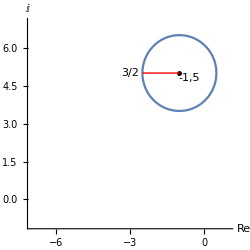

```mathematica
RegionPlot[(x+1)^2+(y-5)^2≤(3/2)^2,{x,-7,1},{y,-1,7},Axes->True,Frame->False,PlotStyle->White,AxesLabel->{"Re","ⅈ"},ImageSize->250,Epilog->{{PointSize[0.014],Point[{-1,5}]},{Red,Line[{{-1,5},{-2.5,5}}]},{Text["3/2",{-3,5}]},{Text["-1,5",{-0.6,4.8}]}}]
```

3.  π < Abs[z - 4 + 2 I] < 3 π

```mathematica
Clear["Global`*"]
```

```mathematica
Abs[z-a]≤ ρ
```

```mathematica
Solve[-4+2 ⅈ==-a,a]
```

{{a→4-2 ⅈ}}

Giving me x=4, y=-2, and an annulus between radius ρ=π and ρ=3 π

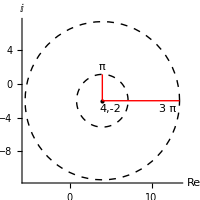

```mathematica
Graphics[{{Dashed,Circle[{4,-2},3π]},{Dashed,Circle[{4,-2},π]},{Point[{4,-2}]},{Red,Line[{{4,-2},{4+3π,-2}}]},{Text["3 π",{12,-3}]},{Text["4,-2",{5,-3}]},{Red,Line[{{4,-2},{4,-2+π}}]},{Text["π",{4,2}]}},Axes->True, ImageSize->200,AxesLabel->{"Re","ⅈ"}]
```

Plot construction using Graphics commands instead of RegionPlot is a little shorter, and also a little easier. The dashed circles represent open sets.

5.  Abs[Arg[z]]<1/4 π

```mathematica
Clear["Global`*"]
```

```mathematica
Abs[z-a]≤ ρ
```

Abs[-a+z]≤ρ

```mathematica
Solve[0-Arg[z]==-a,a]
```

{{a→Arg[z]}}

Giving me x=0, y=Arg[z], and ρ = π/4

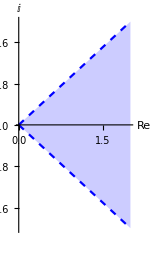

```mathematica
Plot[{x,-x},{x,0,2},ImageSize->150,AspectRatio->1.7,PlotStyle->{{Dashed,Blue},{Dashed,Blue}},Filling->Axis,AxesLabel->{"Re","ⅈ"}]
```

This plot should be considered as that of a quarter circle of infinite radius, centered on the origin, with open boundaries.

7.  Re[z] >= -1

```mathematica
Clear["Global`*"]
```

```mathematica
Abs[z-a]≤ ρ
```

Abs[-a+z]≤ρ

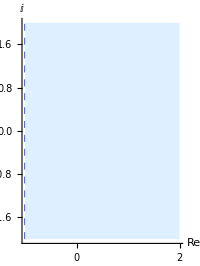

```mathematica
Graphics[{{Dashed,Blue,Thick,Line[{{-1,-2},{-1,2}}]},{LightBlue,Rectangle[{-1,-2},{2,2}]}},Axes->True, ImageSize->200,AxesLabel->{"Re","ⅈ"}]
```

I’m not really sure how to do the above with an equation. I see it as an infinite open semi-circle centered at -1,0.
The real part of z is equal to or greater than -1, and Arg[z] is unrestricted.

10 - 12 Complex functions and their derivatives
Function values. Find Re[f] and Im[f] and their values at the given point z.

11.  f[z_]=1/(1-z) at 1-ⅈ

```mathematica
Clear["Global`*"]
```

```mathematica
f[z_]=1/(1-z)
```

1/(1-z)

```mathematica
dek=f[1-ⅈ]
```

-ⅈ

Or expressed as 0 - 1 (ⅈ). The yellow cell is not given in the text answer, though I believe it satisfies the problem requirement.

14 - 17 Continuity. Find out, and give reason, whether f(z) is continuous at z=0 if f(0)=0 and for z≠0 the function is equal to:

15.  Abs[z]^2 Im[1/z]

```mathematica
Clear["Global`*"]
```

```mathematica
f[z_]=Abs[z]^2 Im[1/z]
```

Abs[z]^2 Im[1/z]

```mathematica
Limit[f[z],z->0]
```

0

Mathematica did not cite difficulties in performing the above limit, so I will take the result as positive. The answers in the text give the reasons.

17. Re[z]/(1-Abs[z])

```mathematica
Clear["Global`*"]
```

```mathematica
f[z]=Re[z]/(1-Abs[z])
```

Re[z]/(1-Abs[z])

```mathematica
Limit[f[z],z->0]
```

0

Again, the limit maneuver did not involve a snag. The answers in the text give the reasons.

18 - 23 Differentiation. Find the value of the derivative of

19.  (z-4 ⅈ)^8    at 3+4 ⅈ

```mathematica
Clear["Global`*"]
```

```mathematica
f[z_]=(z-4 ⅈ)^8
```

(-4 ⅈ+z)^8

```mathematica
dif=D[f[z],z]
```

8 (-4 ⅈ+z)^7

```mathematica
dif1=dif/.z->(3+4 ⅈ)
```

17496

21.  ⅈ(1-z)^n   at 0

```mathematica
Clear["Global`*"]
```

```mathematica
f[z]=ⅈ(1-z)^n
```

ⅈ (1-z)^n

```mathematica
der=D[f[z],z]
```

-ⅈ n (1-z)^(-1+n)

```mathematica
der1=der/.z->(0)
```

-ⅈ n

The above yellow cell does not agree with the text answer (n * ⅈ). However, I ran the problem in Symbolab, and Symbolab agreed with Mathematica's solution.

23.  z^3/(z+ⅈ)^3   at ⅈ

```mathematica
Clear["Global`*"]
```

```mathematica
f[z]=z^3/(z+ⅈ)^3
```

z^3/(ⅈ+z)^3

```mathematica
der=Simplify[D[f[z],z]]
```

(3 ⅈ z^2)/(ⅈ+z)^4

```mathematica
der1=der/.z->ⅈ
```

-(3 ⅈ)/16